{{0.,-0.0998334,-0.198669,-0.29552,-0.389418,-0.479426,-0.564642,-0.644218,-0.717356,-0.783327,-0.841471},{0.0998334,0.,-0.0998334,-0.198669,-0.29552,-0.389418,-0.479426,-0.564642,-0.644218,-0.717356,-0.783327},{0.198669,0.0998334,0.,-0.0998334,-0.198669,-0.29552,-0.389418,-0.479426,-0.564642,-0.644218,-0.717356},{0.29552,0.198669,0.0998334,0.,-0.0998334,-0.198669,-0.29552,-0.389418,-0.479426,-0.564642,-0.644218},{0.389418,0.29552,0.198669,0.0998334,0.,-0.0998334,-0.198669,-0.29552,-0.389418,-0.479426,-0.564642},{0.479426,0.389418,0.29552,0.198669,0.0998334,0.,-0.0998334,-0.198669,-0.29552,-0.389418,-0.479426},{0.564642,0.479426,0.389418,0.29552,0.198669,0.0998334,0.,-0.0998334,-0.198669,-0.29552,-0.389418},{0.644218,0.564642,0.479426,0.389418,0.29552,0.198669,0.0998334,0.,-0.0998334,-0.198669,-0.29552},{0.717356,0.644218,0.564642,0.479426,0.389418,0.29552,0.198669,0.0998334,0.,-0.0998334,-0.198669},{0.783327,0.717356,0.644218,0.564642,0.479426,0.389418,0.29552,0.198669,0.0998334,0.,-0.0998334},{0.841471,0.783327,0.717356,0.644218,0.564642,0.479426,0.389418,0.29552,0.198669,0.0998334,0.}}

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

```mathematica
Module[{data, xmin, xmax, tn, xn, tmin, tmax},
xmin = 0;
xmax = 2 Pi;
tmin = 0;
tmax = 1;
tn = 10;
xn = 100;
data = Table[Sin[x - t] 
,{t,tmin, tmax, (tmax-tmin)/tn}
,{x,xmin,xmax, (xmax-xmin)/xn }
];
ListAnimate[
Table[
ListPlot[
data[[i]], 
PlotRange->{{xmin,xmax},{-1,1}},
Ticks->{Table[k Pi/2, {k,0,4}],Automatic}
],{i,tn}]
]
]
(*data[[1]]*)
```

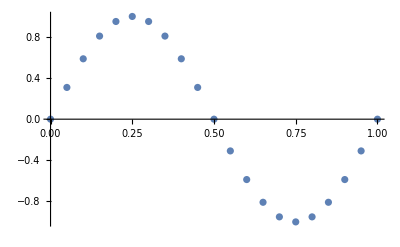

```mathematica
t = Table[{x,Sin[(x-t)(2 Pi)]}
, {t, 0, 1,0.5}
, {x,0,1,1/20}];
ListPlot[t[[1]]]
```

-Graphics-

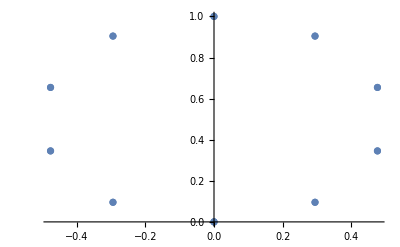

```mathematica
ListPlot[t[[1]]
(*, Ticks->{Table[k Pi/2, {k,0,4}],Automatic}*)
]
ListPlot[#[[2]]{ Cos[2 Pi #[[1]]], Sin[2 Pi #[[1]]] } &/@ t[[1]]]
```